## DIG/CSC 120: Programming in the Humanities Davidson College Dr. Jakub Kabala

Kate, great work here. Pay attention to some styling issues, going forward: your plots should be bigger/more legible (use the ImageSize option); and make sure your labels are meaningful--the x-axis label “Word” is not accurate here.  Also, use Text formatting when writing text (part 3 of problem #2).
A-

## Quiz 7

### Guidelines:

You must work alone.

You have 120 min to complete the quiz. Time begins once you open the Quiz notebook.

This is an open-book quiz: you may consult the Help files in Mathematica, course notes, etc.

Due by Friday March 26th, End of Day in the Moodle Assignment drop.

Fill out the Honor Pledge below

### Honor Pledge (must be signed before you submit):

“I pledge that in completing the problems below I have followed the instructions above and adhered to the standards of the Davidson Honor Code.”

Time & date begun: Thursday, March 25, 2021, 10:20pm
Time & date ended: Thursday, March 25th, 2021, 11:05pm
Total time spent: 45 minutes
Your name: Kate Gilman

### Problem 1

First, define your name, leaving out the spaces. For example:

```mathematica
name="KateGilman"
```

KateGilman

Use a pure function to generate a Row[] of Framed letters in your full name (first and last, no space in-between). Each letter should be in a random color with a size four times that of its letter number (hint: LetterNumber[...]); each frame should have a random background color.

Expected output:

JohnDavidson

```mathematica
Row[Framed[Style[#,RandomColor[],4*LetterNumber[#]],Background->RandomColor[]]&/@Characters[name]]
```

KateGilman

### Problem 2

#### a. Prep: Read Me

Wolfram Mathematica comes with a built-in sentiment classifier that can determine the sentiment (emotion) of a piece of text: either as negative, positive, or neutral. The function you use to do this is Classify[...]. The first argument is the name of the classifier (in our case, “Sentiment”). The second argument is the text whose sentiment we want to classify.

For example (evaluate and study these examples):

```mathematica
Classify["Sentiment","I am having an amazing day"]
```

Positive

```mathematica
Classify["Sentiment","This movie is terrible"]
```

Negative

```mathematica
Classify["Sentiment","Hmm, a bird landed on the table"]
```

Neutral

Underlying these classifications are probabilities, which you can view by adding the term “Probabilities” as a third argument to the function:

```mathematica
Classify["Sentiment","This movie is terrible","Probabilities"]
```

<|Positive→0.062363,Neutral→0.0196967,Negative→0.91794|>

We see that the sentence “This movie is terrible” has a 6% chance of this sentence being positive, a 2% chance of being neutral, and a 92% chance of being negative.

The last output is a data type you haven’t seen yet, one called an Association: it pairs keys (e.g., the term “Positive”), with values (e.g., the number 0.062363). To access any one of the values, you can indicate the key within square brackets at the end, as follows:

```mathematica
Classify["Sentiment","This movie is terrible","Probabilities"]["Positive"]
```

0.062363

Notice that this extracts the value associated with the key “Negative.” Try it out for “Positive” and “Neutral” too.

There is one other function you will need for this problem: MeanFilter[...]. You will use its first syntactical rule.

```mathematica
?MeanFilter
```

In short, MeanFilter[...] allows you to smooth out noisy data by plotting a moving average of that data, the width of which you specify by the second argument. For example, if we start with some noisy data:

```mathematica
randomList=RandomInteger[100,500];(*500 random integers b/w 0-100*)
```

We can smooth it with MeanFilter[...]:

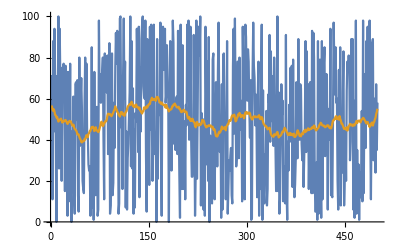

```mathematica
ListLinePlot[
{randomList,(*the noisy data*)
MeanFilter[randomList,25] (*the smoothed out data, using smoothing window of 25*)
}
]
```

You can read more about this function and study its examples in the Help File .

#### b. The Problem!

Download “genesis.txt” from Moodle and import it into your notebook (hint: Import[...]). Save it into a string called ‘genesis’:

```mathematica
genesis=Import["/Users/kate/Downloads/genesis.txt"];
```

This is the text of the Book of Genesis from the Old Testament. Using Classify[...], a pure function, and mapping, create a list of numbers representing the probabilities of each sentence in the Book of Genesis being positive. Since the Book of Genesis has 1197 sentences, you should get a list of 1197 numbers. Review the Classify[...] examples above. Save the result -- your list of 1197 probabilities -- into a symbol called ‘positives’:

```mathematica
positives=Classify["Sentiment",#,"Probabilities"]["Positive"]&/@TextSentences[genesis];
```

Using ‘positives’, the meanFilter[...] function, and another pure function/mapping combination, create a well-styled plot, with a legend, showing the smoothed-out emotional trajectory of the Book of Genesis, at five different smoothing-average windows (100, 200, 300, 400, and 500). Your result should look something like this:

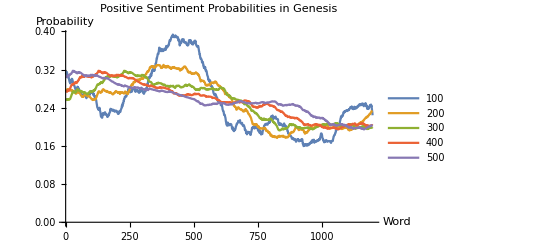

```mathematica
ListLinePlot[MeanFilter[positives,#]&/@{100,200,300,400,500},PlotLegends->{"100","200","300","400","500"},PlotLabel->"Positive Sentiment Probabilities in Genesis",AxesLabel-> {"Word","Probability"},LabelStyle->Directive[Orange,Bold]]
```

Write a few sentences of interpretation about your results. What does the emotional trajectory of the Book of Genesis seem to be?

```mathematica
This tells me that as the book goes on, the probability that the sentence is positive gets overall lower throughout the Book of Genesis. It also tells me that using  higher smoothing-average windows, it makes the line much more direct and straight. It seems like the book gets either more neutral or negative as the book goes on, and that it stays relatively at the same probability of being positive throughout the book, with a slight decline.
```